```mathematica
a=1;b=3;n=10;
```

```mathematica
m=n/2;
```

```mathematica
h=(b-a)/(2m)//N;
```

```mathematica
f[x_]=E^(-2 x^2);
```

```mathematica
prib=h/3(f[a]+2*Sum[f[a+2*i*h],{i,1,m-1}]+4*Sum[f[a+(2i-1)*h],{i,1,m}]+f[b])
```

0.0285359

```mathematica
NIntegrate[f[x],{x,1,3}]
```

0.0285131

```mathematica
cet[x_]=D[f[x],{x,4}]
```

48 ⅇ^(-2 x^2)-384 ⅇ^(-2 x^2) x^2+256 ⅇ^(-2 x^2) x^4

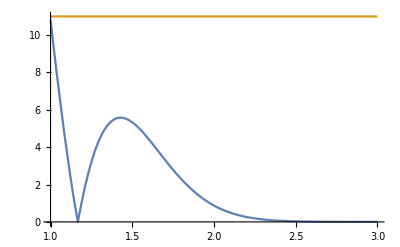

```mathematica
Plot[{Abs[cet[x]],11},{x,1,3}]
```

```mathematica
m4=11
```

11

```mathematica
greska=(b-a)/180*m4*h^4
```

0.000195556

```mathematica
f[x_]=Cos[5x]-12x-0.5
```

-0.5-12 x+Cos[5 x]

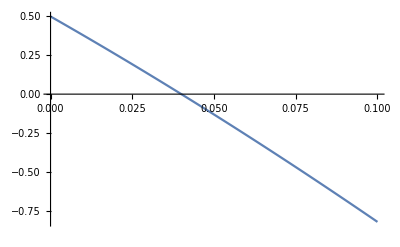

```mathematica
Plot[f[x],{x,0,0.1}]
```

```mathematica
f[0]*f[0.1]<0
```

True

```mathematica
prvi[x_]=D[f[x],x]
```

-12-5 Sin[5 x]

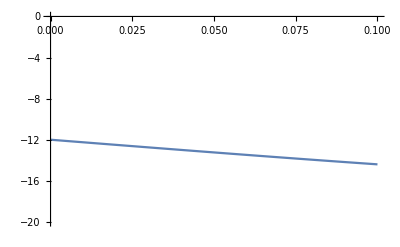

```mathematica
Plot[prvi[x],{x,0,0.1},PlotRange->{-20,0}]
```

```mathematica
(*f'[x]!=0, za xϵ[0,0.1]*)
drugi[x_]=D[f[x],{x,2}]
```

-25 Cos[5 x]

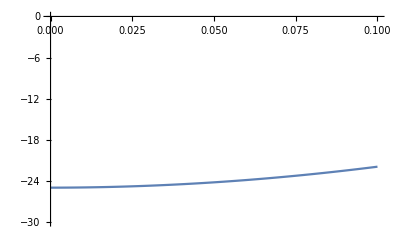

```mathematica
Plot[drugi[x],{x,0,0.1},PlotRange->{-30,0}]
```

```mathematica
(*f"[x]<0, za xϵ[0,0.5]*)
```

```mathematica
f[0]*drugi[0]<0
```

True

```mathematica
f[0.1]*drugi[0.1]>0
```

True

```mathematica
iter[0]=0//N;
```

```mathematica
iter[1]=0.1;
```

```mathematica
i=1;
```

```mathematica
While[Abs[iter[i]-iter[i-1]]>=10^-6,
iter[i+1]=iter[i]-(iter[i]-iter[i-1])/(f[iter[i]]-f[iter[i-1]])f[iter[i]];
i=i+1;
]
```

```mathematica
Table[iter[k],{k,1,i}]
```

{0.1,0.0378095,0.0398903,0.0400054,0.0400051}

```mathematica
a=({{25, -1, 2, -1}, {0, 20, 3, 1}, {-1, -1, 20, 3}, {1, 1, -2, 22}});b=({{2}, {1}, {-1}, {0}});x0=({{1}, {-1}, {1}, {1}});
```

```mathematica
jakobi[a_,b_,x0_,kmax_]:=Module[{},
res={x0};
n=Length[x0];
itnew=x0//N;
Do[
itold=itnew;
Do[
itnew[[i,1]]=-1/a[[i,i]](Sum[a[[i,j]]*itold[[j,1]],{j,1,i-1}]+Sum[a[[i,j]]*itold[[j,1]],{j,i+1,n}]-b[[i,1]]),
{i,1,n}];
res=Append[res,itnew],
{k,0,kmax}];
res
]
```

```mathematica
jakobi[a,b,x0,10]
```

{{{1},{-1},{1},{1}},{{0.},{-0.15},{-0.2},{0.0909091}},{{0.0936364},{0.0754545},{-0.0711364},{-0.0113636}},{{0.0882545},{0.0612386},{-0.0398409},{-0.0141529}},{{0.0850707},{0.0566838},{-0.0404024},{-0.010417}},{{0.0850829},{0.0565812},{-0.0413497},{-0.0101163}},{{0.0851666},{0.0567083},{-0.0413993},{-0.0101983}},{{0.0851723},{0.0567198},{-0.0413765},{-0.0102124}},{{0.0851704},{0.0567171},{-0.0413735},{-0.0102111}},{{0.0851701},{0.0567166},{-0.041374},{-0.0102107}},{{0.0851702},{0.0567166},{-0.0413741},{-0.0102107}},{{0.0851702},{0.0567166},{-0.0413741},{-0.0102107}}}

```mathematica
f[t_,y_]=5y+12t*Cos[2t]
```

```mathematica
5 y+12 Cos[2 t]
```

```mathematica
pok[f_,t_,y_,a_,b_,t0_,y0_,n_]:=Module[{},
ttac[0]=t0;
wit[0]=y0;
h=(b-a)/n//N;
Do[
ttac[i+1]=ttac[i]+h;
wpom=wit[i]+h*f/.{t->ttac[i],y->wit[i]};
wit[i+1]=wit[i]+h/2*(f/.{t->ttac[i],y->wit[i]}+f/.{t->ttac[i+1],y->wpom}),
{i,0,n-1}];
Table[{ttac[i],wit[i]},{i,0,n}]
]
```

```mathematica
pok[f[t,y],t,y,1,2,1,3,20]
```

ReplaceAll::reps: {5 y+12 Cos[2 t]+(t→1),5 y+12 Cos[2 t]+(y→3)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {11.4434+(1.05→1),11.4434+(3.50031→3)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5 y+12 Cos[2 t]+(t→1.05),5 y+12 Cos[2 t]+(y→3+0.025 (11.4434/.{Plus[«2»],Plus[«2»]}))} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$Aborted